```mathematica
Get["https://raw.githubusercontent.com/srossd/SCWIGE/main/Install.m"]
```

```mathematica
Needs["SCWIGE`"]
```

## 𝒩 = 2 Interface

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[U1,{{1,0}}];
SetSignature["Euclidean"];
SetDefectCodimension[1];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"K\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"K\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
alleqs=Join[WardEquations[{"J","ξ"},"Defect"->True],WardEquations[{"J","ξ̄"},"Defect"->True]];
vars=DeleteDuplicates@Cases[alleqs,g[fields_,__][__]/;Total[ScalingDimension/@fields]>4,All];
{b,m}=Normal[CoefficientArrays[alleqs,vars]];
(consistency=NullSpace[Transpose[m]].b//Simplify);
scpVars=Reverse@DeleteDuplicates[Cases[consistency,Derivative[__][g[x__]][y__]:>g[x][y],All]];
consistencySol=Simplify@First@Solve[Thread[consistency==0],{D[scpVars[[1]],u]}];
```

```mathematica
AddSolutions[consistencySol]
```

```mathematica
AddSolutions[SolveWard[{"J","ξ"},"Defect"->True]];
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True]];
```

```mathematica
AddSolutions[SolveWard[{"ξ","K"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ","K̄"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ̄","K"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ̄","K̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","j"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ̄","j"},"Defect"->True]]
```

## 𝒩 = 2 (4,0) Surface Defect

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[SU2];
SetSignature["Euclidean"];
SetDefectCodimension[2,{4,0}];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"K\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"K\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Automated Ward identities and solutions

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->False]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->False]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K̄","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","j"},"Defect"->True,"QBar"->True]];
AddSolutions[SolveWard[{"j","ξ̄"},"Defect"->True]];
```

```mathematica
Normal[SolvedCorrelators[]]/.HoldPattern[key_->value_]:>(key->value[[1]][u,v])/.g[Multiplet[1][[{1,1}]]/.{{2},0}->{2},1,1]->({u,v}|->1/(16 u^2))//FullSimplify
```

{g_(1,1)^(ξ_2(ξ̄)_2)→ⅈ/(64 u^3),g_(1,2)^(ξ_2(ξ̄)_2)→0,g_(1,1)^ξ_2ξ_2→0,g_(1,2)^ξ_2ξ_2→0,g_(1,1)^((ξ̄)_2(ξ̄)_2)→0,g_(1,2)^((ξ̄)_2(ξ̄)_2)→0,g_(1,1)^(K_1(K̄)_1)→1/(64 u^3),g_(1,1)^((K̄)_1(K̄)_1)→0,g_(1,1)^K_1K_1→0,g_(1,1)^j_1j_1→0,g_(1,2)^j_1j_1→0,g_(1,3)^j_1j_1→0,g_(1,4)^j_1j_1→1/(256 u^4),g_(1,5)^j_1j_1→0,g_(1,6)^j_1j_1→0}

### Check N=(4,0) defect

```mathematica
mine=SolvedCorrelators[][[7,1]][u,v]
```

(ⅈ (u^2 (-(g_(1,1)^J_3J_3)^(2,0)(u,v))+(v^2-1) (g_(1,1)^J_3J_3)^(0,2)(u,v)+(-3 u+ⅈ √(1-v^2)-2 v) (g_(1,1)^J_3J_3)^(1,0)(u,v)-v^2 (g_(1,1)^J_3J_3)^(1,1)(u,v)-u v (g_(1,1)^J_3J_3)^(2,0)(u,v)+(g_(1,1)^J_3J_3)^(1,1)(u,v))+(2 √(1-v^2)+ⅈ v) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(8 (√(1-v^2)-ⅈ v))

```mathematica
rules=First@Quiet@Solve[Cosh[ρ]==2u+v&&Exp[I θ]==v-I √(1-v^2),{u,v}]
```

{u→1/4 (-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)+2 cosh(ρ)),v→1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))}

```mathematica
Sinh[ρ]^-2 D[Sinh[ρ]^2 D[Exp[I θ]f[u,v]/.rules,ρ],ρ]+D[Exp[I θ]f[u,v]/.rules,{θ,2}]+Exp[I θ]f[u,v]/.rules
silviu=Simplify[%]/.{ρ->ArcCosh[2u+v],θ->-I Log[v-I √(1-v^2)]}//FullSimplify
```

(1/4 ⅇ^(ⅈ θ) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^4(ρ)+3/2 ⅇ^(ⅈ θ) cosh(ρ) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^2(ρ)) csch^2(ρ)+2 ⅈ ⅇ^(ⅈ θ) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+ⅇ^(ⅈ θ) (-1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+(ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,2)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))))

(-3 v^2+3 ⅈ √(1-v^2) v+2) f^(0,1)(u,v)+ⅈ (√(1-v^2)+ⅈ v) ((v^2-1) f^(0,2)(u,v)-(v^2-1) f^(1,1)(u,v)-3 (u+v) f^(1,0)(u,v)-u (u+v) f^(2,0)(u,v))-f^(1,0)(u,v)

```mathematica
Simplify[8mine-silviu/.g[__]->f]
```

0

## 𝒩 = 2 (2,2) Surface Defect

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[U1,{{1,0}}];
SetSignature["Euclidean"];
SetDefectCodimension[2,{2,2}];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"K\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"K\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Automated Ward identities and solutions

```mathematica
eqs=Join[WardEquations[{"J","ξ̄"},"Defect"->True,"QBar"->False],WardEquations[{"ξ","J"},"Defect"->True,"QBar"->True]];
vars=DeleteDuplicates[Cases[eqs,g[fields_,__][__]/;Total[ScalingDimension/@fields]>4,All]];
```

```mathematica
{bb,mm}=Normal[CoefficientArrays[eqs,vars]];
```

```mathematica
consistency=NullSpace[Transpose[mm]].bb//Simplify;
```

```mathematica
jjs=DeleteDuplicates@Cases[consistency,Derivative[__][g[__]][__],All];
sol=First@Solve[Thread[consistency==0],jjs]
AddSolutions[sol];
```

{(g_(1,1)^J_0J_0)^(1,0)(u,v)→(g_(1,1)^(J_-2J_2))^(1,0)(u,v),(g_(1,1)^J_0J_0)^(0,1)(u,v)→(g_(1,1)^(J_-2J_2))^(0,1)(u,v)+(2 ⅈ (g_(1,1)^(J_-2J_2)(u,v)-g_(1,1)^J_0J_0(u,v)))/(√(1-v^2))}

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->False]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->False]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K̄","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","j"},"Defect"->True,"QBar"->True]];
AddSolutions[SolveWard[{"j","ξ̄"},"Defect"->True]];
```

```mathematica
Normal[SolvedCorrelators[]][[3;;]]/.HoldPattern[key_->value_]:>(key->value[[1]][u,v])/.g[fields_,1,1]/;Total[ScalingDimension/@fields]==4->({u,v}|->1/(16 u^2))//FullSimplify
```

{g_(1,1)^J_0j_0→0,g_(1,2)^J_0j_0→0,g_(1,1)^(ξ_-1(ξ̄)_1)→ⅈ/(64 u^3),g_(1,2)^(ξ_-1(ξ̄)_1)→0,g_(1,1)^(ξ_1(ξ̄)_-1)→ⅈ/(64 u^3),g_(1,2)^(ξ_1(ξ̄)_-1)→0,g_(1,1)^J_0K_0→0,g_(1,1)^(ξ_-1ξ_1)→0,g_(1,2)^(ξ_-1ξ_1)→0,g_(1,1)^(J_0(K̄)_0)→0,g_(1,1)^((ξ̄)_-1(ξ̄)_1)→0,g_(1,2)^((ξ̄)_-1(ξ̄)_1)→0,g_(1,1)^(K_0(K̄)_0)→1/(64 u^3),g_(1,1)^((K̄)_0(K̄)_0)→0,g_(1,1)^K_0K_0→0,g_(1,1)^j_0j_0→0,g_(1,2)^j_0j_0→0,g_(1,3)^j_0j_0→0,g_(1,4)^j_0j_0→1/(256 u^4),g_(1,5)^j_0j_0→0,g_(1,6)^j_0j_0→0}

### Check N=(2,2) defect

```mathematica
mine=SolvedCorrelators[][[15,1]][u,v]
```

(ⅈ (u^2 (-(g_(1,1)^(J_-2J_2))^(2,0)(u,v))+(v^2-1) (g_(1,1)^(J_-2J_2))^(0,2)(u,v)+(-3 u+ⅈ √(1-v^2)-2 v) (g_(1,1)^(J_-2J_2))^(1,0)(u,v)-v^2 (g_(1,1)^(J_-2J_2))^(1,1)(u,v)-u v (g_(1,1)^(J_-2J_2))^(2,0)(u,v)+(g_(1,1)^(J_-2J_2))^(1,1)(u,v))+(2 √(1-v^2)+ⅈ v) (g_(1,1)^(J_-2J_2))^(0,1)(u,v))/(8 (√(1-v^2)-ⅈ v))

```mathematica
rules=First@Quiet@Solve[Cosh[ρ]==2u+v&&Exp[I θ]==v-I √(1-v^2),{u,v}]
```

{u→1/4 (-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)+2 cosh(ρ)),v→1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))}

```mathematica
v-I √(1-v^2)/.rules//FullSimplify
```

cos(θ)-ⅈ √(sin^2(θ))

```mathematica
Sinh[ρ]^-2 D[Sinh[ρ]^2 D[Exp[-I θ]f[u,v]/.rules,ρ],ρ]+D[Exp[-I θ]f[u,v]/.rules,{θ,2}]+Exp[-I θ]f[u,v]/.rules
silviu=Simplify[%]/.{ρ->ArcCosh[2u+v],θ->-I Log[v-I √(1-v^2)]}//FullSimplify
```

(1/4 ⅇ^(-ⅈ θ) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^4(ρ)+3/2 ⅇ^(-ⅈ θ) cosh(ρ) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^2(ρ)) csch^2(ρ)-2 ⅈ ⅇ^(-ⅈ θ) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+ⅇ^(-ⅈ θ) (-1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+(ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,2)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))))

-1/(16 (v-ⅈ √(1-v^2))^3)(-4 (√(1-v^2)+ⅈ v)^4 f^(1,1)(u,v)+(√(1-v^2)+ⅈ v)^4 f^(2,0)(u,v)+24 (√(1-v^2)+ⅈ v)^2 (2 u+v) f^(1,0)(u,v)-8 (√(1-v^2)+ⅈ v)^2 f^(1,1)(u,v)+12 ⅈ (√(1-v^2)+ⅈ v) f^(1,0)(u,v)-8 (v-ⅈ √(1-v^2)) (-3+(v-ⅈ √(1-v^2))^2) f^(0,1)(u,v)+4 (-1+(v-ⅈ √(1-v^2))^2)^2 f^(0,2)(u,v)+4 (v-ⅈ √(1-v^2))^3 f^(1,0)(u,v)+2 (√(1-v^2)+ⅈ v)^2 cosh(2 cosh^-1(2 u+v)) f^(2,0)(u,v)-4 f^(1,1)(u,v)+f^(2,0)(u,v))

```mathematica
FullSimplify[8 mine-silviu/.g[__]->f]
```

0

## 𝒩 = 2 (2,2) Surface Defect - Hypermultiplet

```mathematica
SetGlobalSymmetry[{SU2,SU2,U1}];
SetQGlobalRep[{{0},{1},1}];
SetDefectGlobalSymmetry[U1,{{1,1,0}}];
SetSignature["Euclidean"];
SetDefectCodimension[2,{2,2}];
```

### Hypermultiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"q\", TraditionalForm]\)",{{1},{1},0},1,{0,0},0],Operator["\!\(\*FormBox[\"ζ\", TraditionalForm]\)",{{1},{0},1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ζ\", \"_\"], TraditionalForm]\)",{{1},{0},-1},3/2,{0,1/2},-1]},"Hypermultiplet",True,1]
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Automated Ward identities and solutions

```mathematica
eqs=Join[WardEquations[{"ζ","q"},"Defect"->True,"QBar"->True],WardEquations[{"q","ζ̄"},"Defect"->True,"QBar"->False]];
vars=DeleteDuplicates[Cases[eqs,g[fields_,__][__]/;Total[ScalingDimension/@fields]>2,All]];
```

```mathematica
{bb,mm}=Normal[CoefficientArrays[eqs,vars]];
```

```mathematica
consistency=NullSpace[Transpose[mm]].bb//Simplify;
```

```mathematica
qqs=DeleteDuplicates@Cases[consistency,Derivative[__][g[__]][__],All];
sol=First@Solve[Thread[consistency==0],qqs]
```

{(g_(1,1)^(q_(0_1)q_(0_2)))^(0,1)(u,v)→(g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(ⅈ (g_(1,1)^(q_-2q_2)(u,v)-g_(1,1)^(q_(0_1)q_(0_2))(u,v)))/(√(1-v^2)),(g_(1,1)^(q_(0_1)q_(0_2)))^(1,0)(u,v)→(g_(1,1)^(q_-2q_2))^(1,0)(u,v)}

```mathematica
AddSolutions[sol]
```

```mathematica
AddSolutions[SolveWard[{"ζ","q"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"q","ζ̄"},"Defect"->True,"QBar"->False]]
```

```mathematica
SolvedCorrelators[]
```

<|(g_(1,1)^(q_(0_1)q_(0_2)))^(0,1)→{{u,v}↦(g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(ⅈ (g_(1,1)^(q_-2q_2)(u,v)-g_(1,1)^(q_(0_1)q_(0_2))(u,v)))/(√(1-v^2))},(g_(1,1)^(q_(0_1)q_(0_2)))^(1,0)→{{u,v}↦(g_(1,1)^(q_-2q_2))^(1,0)(u,v)},g_(1,1)^(ζ_-1(ζ̄)_1)→{{u,v}↦(ⅈ √(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(-u-ⅈ √(1-v^2)-v) (g_(1,1)^(q_-2q_2))^(1,0)(u,v)-g_(1,1)^(q_-2q_2)(u,v))/(4 (√(1-v^2)-ⅈ v))},g_(1,2)^(ζ_-1(ζ̄)_1)→{{u,v}↦(√(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+ⅈ g_(1,1)^(q_-2q_2)(u,v)+ⅈ u (g_(1,1)^(q_-2q_2))^(1,0)(u,v))/(-4 √(1-v^2)+4 ⅈ v)},g_(1,1)^(ζ_1(ζ̄)_-1)→{{u,v}↦(ⅈ √(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(-u-ⅈ √(1-v^2)-v) (g_(1,1)^(q_-2q_2))^(1,0)(u,v)-g_(1,1)^(q_-2q_2)(u,v))/(4 (√(1-v^2)-ⅈ v))},g_(1,2)^(ζ_1(ζ̄)_-1)→{{u,v}↦(√(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+ⅈ g_(1,1)^(q_-2q_2)(u,v)+ⅈ u (g_(1,1)^(q_-2q_2))^(1,0)(u,v))/(-4 √(1-v^2)+4 ⅈ v)}|>

## 𝒩 = 2 Line Defect

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[SU2];
SetSignature["Euclidean"];
SetDefectCodimension[3,0];
```

### Vector multiplet

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[\"φ\", TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{{0},2},2,{1,0},2]},{Operator["\!\(\*FormBox[OverscriptBox[\"φ\", \"_\"], TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-1},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{{0},-2},2,{0,1},-2]}},"Vector",False,1]
```

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,3];
```

```mathematica
DisplaySUSYVariations[]
```

1

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
Do[SetTwoPtGlobalInvariant[rep,ConjugateIrrep[GlobalSymmetry[],rep],SparseArray@IdentityMatrix[Times@@DimR[GlobalSymmetry[],rep]]],{rep,GlobalRep/@Multiplet[1]}]
SetTwoPtGlobalInvariant[{0},{0},SparseArray@IdentityMatrix[1]];
SetTwoPtGlobalInvariant[{2},{2},SparseArray@IdentityMatrix[3]]
SetTwoPtGlobalInvariant[{1},{1},LeviCivitaTensor[2]]
SetTwoPtGlobalInvariant[{1},AlternateRep[{1}],IdentityMatrix[2]]
SetTwoPtGlobalInvariant[AlternateRep[{1}],AlternateRep[{1}],LeviCivitaTensor[2]]
```

```mathematica
SetThreePtGlobalInvariant[{{2},0},{{1},1},{{1},-1},SparseArray[(PauliMatrix/@Range[3])]]
SetThreePtGlobalInvariant[{{0},-2},{{1},1},{{1},1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},2},{{1},-1},{{1},-1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},0},{{1},1},{{1},-1},SparseArray[{IdentityMatrix[2]}]]

SetThreePtGlobalInvariant[{2},{1},{1},SparseArray[(PauliMatrix[#].LeviCivitaTensor[2])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},{1},AlternateRep[{1}],SparseArray[(PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},AlternateRep[{1}],AlternateRep[{1}],SparseArray[(LeviCivitaTensor[2].PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{0},{1},{1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{0},{1},AlternateRep[{1}],SparseArray[{IdentityMatrix[2]}]]
SetThreePtGlobalInvariant[{0},AlternateRep[{1}],AlternateRep[{1}],SparseArray[{LeviCivitaTensor[2]}]]
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Sign testing

```mathematica
pairs={{"ϕ","χ"},{"ϕ","χ̄"},{"χ","Σ"},{"χ","Σ̄"},{"χ̄","Σ"},{"χ̄","Σ̄"}};
Clear[eqExpr];
eqExpr[pair_]:=eqExpr[pair]=ExpandCorrelator@Correlator[NormalOrder[TensorProduct[QTensor[]+Contract[TensorProduct[TwoPtGlobalInvariant[{2,1},{2,1}],σLowerSingle[4],ϵUpperDot,QTensor["QBar"->True]],{{2,7},{4,5},{6,8}}],Tensor[pair]],"Vacuum"->True],"Defect"->True];
signs[pair_]:=Module[{expr,structs},
expr=eqExpr[pair];
structs=DeleteDuplicates[{RPart[#],First@Cases[#,g[fields_,_,_]:>fields[[;;,1]],All,Heads->True]}&/@(List@@expr)];
Table[Labeled[Style[UndirectedEdge[pair,s[[2]]],If[ArrayRules[Flatten[Normal[CanonicallyOrderedComponents[s[[1]]]]]][[1,2]]>0,Black,Orange]],Style[s[[1]],Background->White]],{s,structs}]
]
```

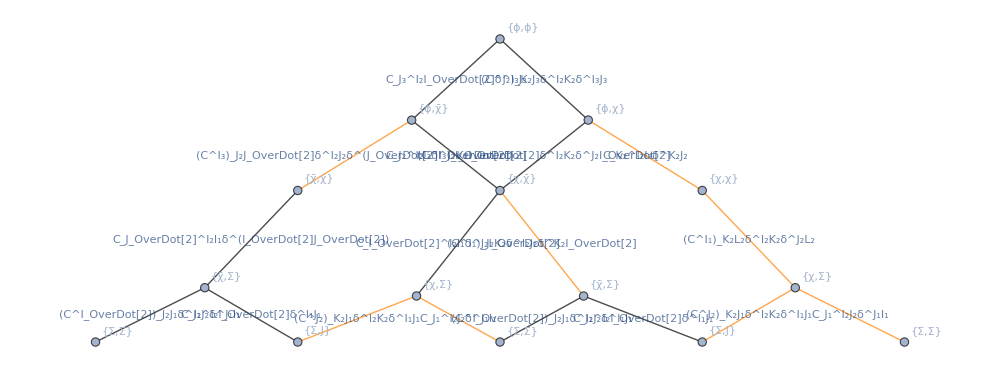

```mathematica
EdgeTaggedGraph[Join@@(signs/@pairs),VertexLabels->Automatic,VertexCoordinates->Thread[Tuples[Multiplet[2][[;;,1]],2]->({2(Last[#[[1]]]+Last[#[[2]]]),-3(ScalingDimension[#[[1]]]+ScalingDimension[#[[2]]])}&/@Tuples[Multiplet[2],2])],ImageSize->1000]
```

#### Automated Ward identities and solutions

```mathematica
AddSolutions[SolveWard[{"ϕ","χ"},"Defect"->True]]
AddSolutions[SolveWard[{"ϕ","χ̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ̄","Σ"},"Defect"->True]]
AddSolutions[SolveWard[{"χ","Σ"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ̄"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","Σ̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","J"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","J"},"Defect"->True]]
```

```mathematica
tt=Exp[-2I φ]g[Multiplet[1][[{6,6}]],1,1][u,v]+2g[Multiplet[1][[{5,6}]],1,1][u,v]+Exp[2I φ]g[Multiplet[1][[{5,5}]],1,1][u,v]/.{{0},_}->{0}
```

2 g_(1,1)^(Σ_1(Σ̄)_1)(u,v)+ⅇ^(-2 ⅈ φ) g_(1,1)^((Σ̄)_1(Σ̄)_1)(u,v)+ⅇ^(2 ⅈ φ) g_(1,1)^Σ_1Σ_1(u,v)

```mathematica
hSolved=Collect[tt/.(First/@SolvedCorrelators[])/.g[Multiplet[1][[{1,1}]]/.{{2},_}->{2},1,1]->a,Derivative[__][a][__],FullSimplify]
%/.{u->U,v->V}//InputForm
```

1/4 a^(1,0)(u,v) (4 u^2-4 u (u+v) cos(2 φ)+6 u v+3 v^2-1)+1/4 a^(0,1)(u,v) ((2 u v-v^2+1) cos(2 φ)-2 u v-3 v^2+1)-1/4 (v^2-1) a^(0,2)(u,v) (u (-cos(2 φ))+u+v)+1/4 (v^2-1) a^(1,1)(u,v) (u (-cos(2 φ))+u+v)-1/4 u (u+v) a^(2,0)(u,v) (u cos(2 φ)-u-v)+1/2 a(u,v) (u-(u+v) cos(2 φ))

(a[U, V]*(U - (U + V)*Cos[2*φ]))/2 + ((1 - 2*U*V - 3*V^2 + (1 + 2*U*V - V^2)*Cos[2*φ])*Derivative[0, 1][a][U, V])/4 - 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[0, 2][a][U, V])/4 + 
 ((-1 + 4*U^2 + 6*U*V + 3*V^2 - 4*U*(U + V)*Cos[2*φ])*Derivative[1, 0][a][U, V])/4 + 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[1, 1][a][U, V])/4 - 
 (U*(U + V)*(-U - V + U*Cos[2*φ])*Derivative[2, 0][a][U, V])/4

```mathematica
Table[{k->SolvedCorrelators[][k][[1]][u,v]/.g[Multiplet[1][[{1,1}]]/.{{2},_}->{2},1,1]->({u,v}|->1/(16 u^2))},{k,Keys[SolvedCorrelators[]]}]//Simplify
```

{{g_(1,1)^(χ_2(χ̄)_2)→ⅈ/(64 u^3)},{g_(1,2)^(χ_2(χ̄)_2)→0},{g_(1,3)^(χ_2(χ̄)_2)→0},{g_(1,4)^(χ_2(χ̄)_2)→0},{g_(1,1)^χ_2χ_2→0},{g_(1,2)^χ_2χ_2→0},{g_(1,3)^χ_2χ_2→0},{g_(1,4)^χ_2χ_2→0},{g_(1,1)^((χ̄)_2(χ̄)_2)→0},{g_(1,2)^((χ̄)_2(χ̄)_2)→0},{g_(1,3)^((χ̄)_2(χ̄)_2)→0},{g_(1,4)^((χ̄)_2(χ̄)_2)→0},{g_(1,1)^Σ_1J_1→0},{g_(1,2)^Σ_1J_1→0},{g_(1,3)^Σ_1J_1→0},{g_(1,4)^Σ_1J_1→0},{g_(1,1)^(Σ_1(Σ̄)_1)→1/(64 u^3)},{g_(1,1)^Σ_1Σ_1→0},{g_(1,1)^((Σ̄)_1J_1)→0},{g_(1,2)^((Σ̄)_1J_1)→0},{g_(1,3)^((Σ̄)_1J_1)→0},{g_(1,4)^((Σ̄)_1J_1)→0},{g_(1,1)^((Σ̄)_1(Σ̄)_1)→0},{g_(1,1)^J_1J_1→0},{g_(1,2)^J_1J_1→0},{g_(1,3)^J_1J_1→0},{g_(1,4)^J_1J_1→0},{g_(1,5)^J_1J_1→0},{g_(1,6)^J_1J_1→0},{g_(1,7)^J_1J_1→0},{g_(1,8)^J_1J_1→0},{g_(1,9)^J_1J_1→0},{g_(1,10)^J_1J_1→0},{g_(1,11)^J_1J_1→0},{g_(1,12)^J_1J_1→0},{g_(1,13)^J_1J_1→1/(256 u^4)},{g_(1,14)^J_1J_1→0},{g_(1,15)^J_1J_1→0},{g_(1,16)^J_1J_1→0}}

```mathematica
Normal[SolvedCorrelators[]][[-23]]
Collect[8 u^2%[[2,1]][u,v]/.g[__]->Function[{u,v},a[u,v]/(u(u+v))],a[u,v]|Derivative[__][a][__],FullSimplify]
```

g_(1,1)^(ΣΣ̄)→{{u,v}↦1/8 (u^3 (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 u^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)-v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)-u v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+(-2 u v-3 v^2+1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+3 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u g_(1,1)^ϕϕ(u,v)+u (g_(1,1)^ϕϕ)^(0,2)(u,v)+6 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)-u (g_(1,1)^ϕϕ)^(1,1)(u,v)+v (g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,0)(u,v)-v (g_(1,1)^ϕϕ)^(1,1)(u,v))}

u^2 (u+v) a^(2,0)(u,v)+u (v^2-1) a^(1,1)(u,v)+(u-u v^2) a^(0,2)(u,v)+(1-v (2 u+v)) a^(0,1)(u,v)

```mathematica
Normal[SolvedCorrelators[]][[-22]]
Collect[8 u^2%[[2,1]][u,v]/.g[__]->Function[{u,v},a[u,v]/u^2],a[u,v]|Derivative[__][a][__],Simplify]
```

g_(1,1)^ΣΣ→{{u,v}↦1/8 (u (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+(-2 u v+v^2-1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+2 (u+v) g_(1,1)^ϕϕ(u,v))}

u^2 (u+v) a^(2,0)(u,v)+u (v^2-1) a^(1,1)(u,v)+(-2 u v-v^2+1) a^(0,1)(u,v)+(u-u v^2) a^(0,2)(u,v)

```mathematica
SolvedCorrelators[]//Normal//TableForm
```

g_(1,1)^(χ_2(χ̄)_2)→{{u,v}↦1/8 ⅈ ((g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,2)^(χ_2(χ̄)_2)→{{u,v}↦1/8 ⅈ v (2 g_(1,1)^ϕ_3ϕ_3(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,3)^(χ_2(χ̄)_2)→{{u,v}↦0}
g_(1,4)^(χ_2(χ̄)_2)→{{u,v}↦0}
g_(1,1)^χ_2χ_2→{{u,v}↦0}
g_(1,2)^χ_2χ_2→{{u,v}↦0}
g_(1,3)^χ_2χ_2→{{u,v}↦-1/8 ⅈ (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)}
g_(1,4)^χ_2χ_2→{{u,v}↦-1/8 ⅈ v (2 g_(1,1)^ϕ_3ϕ_3(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,1)^((χ̄)_2(χ̄)_2)→{{u,v}↦0}
g_(1,2)^((χ̄)_2(χ̄)_2)→{{u,v}↦0}
g_(1,3)^((χ̄)_2(χ̄)_2)→{{u,v}↦-1/8 ⅈ (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)}
g_(1,4)^((χ̄)_2(χ̄)_2)→{{u,v}↦-1/8 ⅈ v (2 g_(1,1)^ϕ_3ϕ_3(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,1)^Σ_1J_1→{{u,v}↦0}
g_(1,2)^Σ_1J_1→{{u,v}↦0}
g_(1,3)^Σ_1J_1→{{u,v}↦-(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+4 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-2 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(16 √6)}
g_(1,4)^Σ_1J_1→{{u,v}↦(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+2 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-4 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(8 √6)}
g_(1,1)^(Σ_1(Σ̄)_1)→{{u,v}↦1/8 (u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+(-2 u v-3 v^2+1) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 u g_(1,1)^ϕ_3ϕ_3(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+6 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))}
g_(1,1)^Σ_1Σ_1→{{u,v}↦1/8 (-u (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+(2 u v-v^2+1) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-2 (u+v) g_(1,1)^ϕ_3ϕ_3(u,v))}
g_(1,1)^((Σ̄)_1J_1)→{{u,v}↦0}
g_(1,2)^((Σ̄)_1J_1)→{{u,v}↦0}
g_(1,3)^((Σ̄)_1J_1)→{{u,v}↦(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+4 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-2 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(16 √6)}
g_(1,4)^((Σ̄)_1J_1)→{{u,v}↦(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+2 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-4 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(8 √6)}
g_(1,1)^((Σ̄)_1(Σ̄)_1)→{{u,v}↦1/8 (-u (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+(2 u v-v^2+1) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-2 (u+v) g_(1,1)^ϕ_3ϕ_3(u,v))}
g_(1,1)^J_1J_1→{{u,v}↦(v^2 (-2 v (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+2 v^3 ((g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+v^2 (4 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-6 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v))+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(384 u)}
g_(1,2)^J_1J_1→{{u,v}↦-(v^2 (4 u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+16 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+6 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+4 u (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+20 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (2 u+v) g_(1,1)^ϕ_3ϕ_3(u,v)-4 v (2 u+v) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)))/(384 u)}
g_(1,3)^J_1J_1→{{u,v}↦0}
g_(1,4)^J_1J_1→{{u,v}↦0}
g_(1,5)^J_1J_1→{{u,v}↦(v^2 (-2 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+(8 v^2-6) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+4 v g_(1,1)^ϕ_3ϕ_3(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-4 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(384 u)}
g_(1,6)^J_1J_1→{{u,v}↦0}
g_(1,7)^J_1J_1→{{u,v}↦0}
g_(1,8)^J_1J_1→{{u,v}↦(v^2 (-4 u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-8 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-6 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+2 (8 u v+4 v^2-3) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-16 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (2 u+v) g_(1,1)^ϕ_3ϕ_3(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)))/(384 u)}
g_(1,9)^J_1J_1→{{u,v}↦0}
g_(1,10)^J_1J_1→{{u,v}↦0}
g_(1,11)^J_1J_1→{{u,v}↦0}
g_(1,12)^J_1J_1→{{u,v}↦0}
g_(1,13)^J_1J_1→{{u,v}↦(2 u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+8 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+4 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+(-4 u v-6 v^2+3) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+4 u g_(1,1)^ϕ_3ϕ_3(u,v)+2 u (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+12 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))/(96 u)}
g_(1,14)^J_1J_1→{{u,v}↦0}
g_(1,15)^J_1J_1→{{u,v}↦0}
g_(1,16)^J_1J_1→{{u,v}↦(2 u (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+(-4 u v+2 v^2-3) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+4 (u+v) g_(1,1)^ϕ_3ϕ_3(u,v))/(96 u)}

## 𝒩 = 2

```mathematica
SetGlobalSymmetry[{SU2,U1}]
SetSignature["Euclidean"];
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Flavor",True,1];
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,2];
SetMultiplet[{Operator["\!\(\*FormBox[\"M\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ζ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ζ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"Z\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Z\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[\"j1\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"j2\", TraditionalForm]\)",{{2},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"κ\", TraditionalForm]\)",{{1},1},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"κ\", \"_\"], TraditionalForm]\)",{{1},-1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{{0},0},4,{1,1},0]},"Stress Tensor",True,3];
```

```mathematica
DisplaySUSYVariations[]
```

123

### Determine ⟨ϕϕϕϕ⟩

```mathematica
eqs=WardEquations[{"ϕ","ϕ","ϕ","χ̄"}]
```

{2 √2 v^3 g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-2 √2 g_(1,2)^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)+(√2 u g_(1,1)^(ϕϕχχ̄)(v/u,1/u))/v^2-√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-(√2 g_(1,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_(1,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)-((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_(3,1)^ϕϕϕϕ(u,v))/(√2)==0,-2 √2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) v^3-(2 √2 g_(2,2)^(ϕϕχχ̄)(u,v) v^3)/u^3==0,(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/u-√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)+√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)+(√2 g_(2,2)^(ϕϕχχ̄)(u,v))/u^2+(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/v+(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ √(3/2) g_(1,1)^ϕϕϕJ(u,v))/(v u)==0,-(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)+(g_(2,1)^(ϕϕχχ̄)(u,v))/(√2)-((u-1) g_(2,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0,(2 √2 g_(1,2)^(ϕϕχχ̄)(u,v) v^3)/u^3+2 √2 g_(2,2)^(ϕϕχχ̄)(1/u,v/u) v^3==0,-(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/u-(√2 g_(1,2)^(ϕϕχχ̄)(u,v))/u^2+√2 u g_(2,1)^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_(2,2)^(ϕϕχχ̄)(1/u,v/u)+(ⅈ (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_(2,2)^(ϕϕχχ̄)(1/u,v/u) u^2+(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/v+(ⅈ (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)+(ⅈ √(3/2) g_(1,1)^ϕϕϕJ(u,v))/(v u)==0,(g_(2,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_(2,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_(1,1)^ϕϕϕϕ(u,v))/(√2)-(g_(1,1)^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_(1,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0,2 √2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) v^3+(2 √2 g_(1,2)^(ϕϕχχ̄)(u,v) v^3)/u^3-2 √2 g_(2,2)^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-(√2 g_(1,2)^(ϕϕχχ̄)(u,v))/u^2+(√2 u g_(2,1)^(ϕϕχχ̄)(v/u,1/u))/v^2+(ⅈ (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(√2 g_(2,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+(ⅈ (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_(2,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)+(ⅈ g_(1,1)^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)-(g_(1,1)^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_(1,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0}

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,3}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v]}]
```

{g_(1,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(3)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_(1,2)^(ϕϕχχ̄)(1/u,v/u),g_(1,2)^(ϕϕχχ̄)(v/u,1/u),g_(1,1)^(ϕϕχχ̄)(1/u,v/u),g_(1,1)^(ϕϕχχ̄)(v/u,1/u),g_(2,2)^(ϕϕχχ̄)(u,v),g_(1,2)^ϕϕϕJ(u,v),g_(1,1)^ϕϕϕJ(u,v),g_(2,1)^(ϕϕχχ̄)(u,v),g_(1,2)^(ϕϕχχ̄)(u,v),g_(2,2)^(ϕϕχχ̄)(1/u,v/u),g_(2,1)^(ϕϕχχ̄)(1/u,v/u),g_(1,1)^(ϕϕχχ̄)(u,v),g_(2,2)^(ϕϕχχ̄)(v/u,1/u),g_(2,1)^(ϕϕχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify)
```

{1/(2 √2 u)ⅈ (u (u 𝒯^(0,1)(u,v) f(1)(u,v)+((u-v) 𝒯^(0,1)(u,v)+(u-v+1) 𝒯^(1,0)(u,v)) f(2)(u,v)-(v 𝒯^(0,1)(u,v)+(u+v-1) 𝒯^(1,0)(u,v)) f(3)(u,v))+𝒯(u,v) (-2 (u-v+1) f(2)(u,v)+2 (v-1) f(3)(u,v)+u (u (f(1))^(0,1)(u,v)+(u-v) (f(2))^(0,1)(u,v)-v (f(3))^(0,1)(u,v)+u (f(2))^(1,0)(u,v)-v (f(2))^(1,0)(u,v)+(f(2))^(1,0)(u,v)-u (f(3))^(1,0)(u,v)-v (f(3))^(1,0)(u,v)+(f(3))^(1,0)(u,v)))),1/(√2 u v)ⅈ (u ((𝒯^(0,1)(u,v)+𝒯^(1,0)(u,v)) (-f(2)(u,v))+(v 𝒯^(0,1)(u,v)+(u-1) 𝒯^(1,0)(u,v)) f(3)(u,v)+((v-1) 𝒯^(0,1)(u,v)+u 𝒯^(1,0)(u,v)) f(1)(u,v))+𝒯(u,v) (2 f(2)(u,v)+2 f(3)(u,v)+u ((v-1) (f(1))^(0,1)(u,v)-(f(2))^(0,1)(u,v)+v (f(3))^(0,1)(u,v)+u (f(1))^(1,0)(u,v)-(f(2))^(1,0)(u,v)+u (f(3))^(1,0)(u,v)-(f(3))^(1,0)(u,v))))}

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform
```

{ⅈ (-2 (u-v+1) (α(2)+β(2) u+γ(2) v)+2 (v-1) (α(3)+β(3) u+γ(3) v)+u (β(2)+β(3)+β(2) u-β(3) u+γ(1) u+γ(2) (u-v)-β(2) v-β(3) v-γ(3) v))==0,ⅈ (2 (α(2)+β(2) u+γ(2) v)+2 (α(3)+β(3) u+γ(3) v)+u (-β(2)-β(3)-γ(2)+β(1) u+β(3) u+γ(1) (v-1)+γ(3) v))==0,ⅈ (u^2 (α(2)+β(2) u+γ(2) v)-u^2 (α(3)+β(3) u+γ(3) v)-u v (α(2)+β(2) u+γ(2) v)+u (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v)+u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(3)+β(3) u+γ(3) v)-u (α(2)+β(2) u+γ(2) v)-u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(2)+β(2) u+γ(2) v)-u v (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v))==0,ⅈ (-u (α(1)+β(1) u+γ(1) v)+u v (α(1)+β(1) u+γ(1) v)-u (α(2)+β(2) u+γ(2) v)+u v (α(3)+β(3) u+γ(3) v))==0}

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(2)→-α(1),α(3)→α(1),β(1)→-α(1),β(2)→α(1),β(3)→α(1),γ(1)→α(1),γ(2)→α(1),γ(3)→-α(1)}

```mathematica
Table[f[i][u,v],{i,3}]/.fform/.coeffSol/.α[1]->1
```

{-u+v+1,u+v-1,u-v+1}

### Find ,

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],(v/u)^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],u^-1 𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],u^-1 v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],u^-2 v 𝒯[u,v]];
```

```mathematica
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,3}]->{(1-u+v) 𝒯[u,v],(u+v-1)𝒯[u,v],(u-v+1)𝒯[u,v]}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","ϕ","χ̄"}]]
```

```mathematica
SolvedCorrelators[]
```

<|g_(1,1)^ϕϕϕϕ→{{u,v}↦(-u+v+1) 𝒯(u,v)},g_(2,1)^ϕϕϕϕ→{{u,v}↦(u+v-1) 𝒯(u,v)},g_(3,1)^ϕϕϕϕ→{{u,v}↦(u-v+1) 𝒯(u,v)},g_(1,1)^ϕϕϕJ→{{u,v}↦-(u ((u-v+2) 𝒯(u,v)+(u-v+1) v 𝒯^(0,1)(u,v)+u (u-v-1) 𝒯^(1,0)(u,v)))/(√3)},g_(1,2)^ϕϕϕJ→{{u,v}↦((u-2 v+2) 𝒯(u,v)+2 u v 𝒯^(0,1)(u,v)+u (u+v-1) 𝒯^(1,0)(u,v))/(√3)},g_(1,1)^(ϕϕχχ̄)→{{u,v}↦ⅈ (2 𝒯(u,v)+u v 𝒯^(0,1)(u,v)+(u-1) u 𝒯^(1,0)(u,v))},g_(1,2)^(ϕϕχχ̄)→{{u,v}↦ⅈ u (v 𝒯^(0,1)(u,v)+u 𝒯^(1,0)(u,v))},g_(2,1)^(ϕϕχχ̄)→{{u,v}↦ⅈ (-2 (v-1) 𝒯(u,v)+u v 𝒯^(0,1)(u,v)+u (u+v-1) 𝒯^(1,0)(u,v))},g_(2,2)^(ϕϕχχ̄)→{{u,v}↦ⅈ u (u 𝒯^(1,0)(u,v)-𝒯(u,v))},g_(1,1)^ϕϕJJ→{{u,v}↦1/6 ((-2 v^2+8 v+u (v-2)+6) 𝒯(u,v)+v (-2 v^2+u (5 v+3)+2) 𝒯^(0,1)(u,v)+u (𝒯^(1,1)(u,v) v^3+2 (v+1) 𝒯^(0,2)(u,v) v^2+3 u 𝒯^(1,1)(u,v) v^2+u 𝒯^(2,0)(u,v) v^2+u 𝒯^(1,1)(u,v) v-𝒯^(1,1)(u,v) v+u^2 𝒯^(2,0)(u,v) v+2 u 𝒯^(2,0)(u,v) v+(u-2) (3 v+2) 𝒯^(1,0)(u,v)-u^2 𝒯^(2,0)(u,v)+u 𝒯^(2,0)(u,v)))},g_(1,2)^ϕϕJJ→{{u,v}↦1/6 u ((u (2 𝒯^(0,2)(u,v)+𝒯^(1,1)(u,v))-2 𝒯^(0,1)(u,v)) v^2+((5 u+6) 𝒯^(0,1)(u,v)+u (3 (u-1) 𝒯^(1,1)(u,v)+u 𝒯^(2,0)(u,v))) v+(u-2 v+4) 𝒯(u,v)+u ((3 u-1) 𝒯^(1,0)(u,v)+(u-1) u 𝒯^(2,0)(u,v)))},g_(1,3)^ϕϕJJ→{{u,v}↦-1/6 u ((u (2 𝒯^(0,2)(u,v)+𝒯^(1,1)(u,v))-2 𝒯^(0,1)(u,v)) v^2+((5 u+6) 𝒯^(0,1)(u,v)+u (3 (u-1) 𝒯^(1,1)(u,v)+u 𝒯^(2,0)(u,v))) v+(u-2 v+4) 𝒯(u,v)+u ((3 u-1) 𝒯^(1,0)(u,v)+(u-1) u 𝒯^(2,0)(u,v)))},g_(1,4)^ϕϕJJ→{{u,v}↦-1/6 u^2 (𝒯^(1,1)(u,v) u^2+2 𝒯^(2,0)(u,v) u^2+v 𝒯^(0,2)(u,v) u+3 𝒯^(1,0)(u,v) u+3 v 𝒯^(1,1)(u,v) u-𝒯^(1,1)(u,v) u-𝒯(u,v)+(2 u+v+3) 𝒯^(0,1)(u,v)+v^2 𝒯^(0,2)(u,v)+v 𝒯^(0,2)(u,v))},g_(1,5)^ϕϕJJ→{{u,v}↦1/6 u ((u-2 v+2) 𝒯(u,v)+(-2 v^2+u (5 v+3)+2) 𝒯^(0,1)(u,v)+u (𝒯^(2,0)(u,v) u^2+3 v 𝒯^(1,1)(u,v) u+𝒯^(1,1)(u,v) u+v 𝒯^(2,0)(u,v) u+𝒯^(2,0)(u,v) u+2 v (v+1) 𝒯^(0,2)(u,v)+(3 u-2) 𝒯^(1,0)(u,v)+v^2 𝒯^(1,1)(u,v)-𝒯^(1,1)(u,v)))},g_(1,6)^ϕϕJJ→{{u,v}↦-1/6 v ((u-2 v+2) 𝒯(u,v)+(-2 v^2+u (5 v+3)+2) 𝒯^(0,1)(u,v)+u (𝒯^(2,0)(u,v) u^2+3 v 𝒯^(1,1)(u,v) u+𝒯^(1,1)(u,v) u+v 𝒯^(2,0)(u,v) u+𝒯^(2,0)(u,v) u+2 v (v+1) 𝒯^(0,2)(u,v)+(3 u-2) 𝒯^(1,0)(u,v)+v^2 𝒯^(1,1)(u,v)-𝒯^(1,1)(u,v)))},g_(1,1)^(ϕχχ̄J)→{{u,v}↦-(ⅈ u^(3/2) (𝒯^(1,1)(u,v) u^2+𝒯^(2,0)(u,v) u^2+v 𝒯^(0,2)(u,v) u+𝒯^(1,0)(u,v) u+v 𝒯^(1,1)(u,v) u-𝒯^(1,1)(u,v) u-𝒯(u,v)+(2 u-v+3) 𝒯^(0,1)(u,v)+v 𝒯^(0,2)(u,v)))/(2 √3),{u,v}↦-(ⅈ u^(3/2) (𝒯^(1,1)(u,v) u^2+𝒯^(2,0)(u,v) u^2+v 𝒯^(0,2)(u,v) u+𝒯^(1,0)(u,v) u+v 𝒯^(1,1)(u,v) u-𝒯^(1,1)(u,v) u-𝒯(u,v)+(2 u-v+3) 𝒯^(0,1)(u,v)+v 𝒯^(0,2)(u,v)))/(2 √3)},g_(1,2)^(ϕχχ̄J)→{{u,v}↦(ⅈ √u ((3 u-2 v+2) 𝒯^(0,1)(u,v)+u (2 v 𝒯^(0,2)(u,v)-𝒯^(1,0)(u,v)+u 𝒯^(1,1)(u,v)+v 𝒯^(1,1)(u,v)-𝒯^(1,1)(u,v)+u 𝒯^(2,0)(u,v))))/(2 √3),{u,v}↦(ⅈ √u ((3 u-2 v+2) 𝒯^(0,1)(u,v)+u (2 v 𝒯^(0,2)(u,v)-𝒯^(1,0)(u,v)+u 𝒯^(1,1)(u,v)+v 𝒯^(1,1)(u,v)-𝒯^(1,1)(u,v)+u 𝒯^(2,0)(u,v))))/(2 √3)},g_(1,3)^(ϕχχ̄J)→{{u,v}↦(ⅈ √u (2 (u-2 v+1) 𝒯(u,v)+2 (3 u-2 v+1) v 𝒯^(0,1)(u,v)+u (2 𝒯^(0,2)(u,v) v^2+(2 u+2 v-1) 𝒯^(1,1)(u,v) v+2 u 𝒯^(2,0)(u,v) v+(2 u-1) 𝒯^(1,0)(u,v))))/(2 √3),{u,v}↦(ⅈ √u (2 (u-2 v+1) 𝒯(u,v)+2 (3 u-2 v+1) v 𝒯^(0,1)(u,v)+u (2 𝒯^(0,2)(u,v) v^2+(2 u+2 v-1) 𝒯^(1,1)(u,v) v+2 u 𝒯^(2,0)(u,v) v+(2 u-1) 𝒯^(1,0)(u,v))))/(2 √3)},g_(1,4)^(ϕχχ̄J)→{{u,v}↦(ⅈ √u (-2 𝒯(u,v)-2 v 𝒯^(0,1)(u,v)+u (𝒯^(1,0)(u,v)+v 𝒯^(1,1)(u,v))))/(2 √3),{u,v}↦(ⅈ √u (-2 𝒯(u,v)-2 v 𝒯^(0,1)(u,v)+u (𝒯^(1,0)(u,v)+v 𝒯^(1,1)(u,v))))/(2 √3)},g_(1,5)^(ϕχχ̄J)→{{u,v}↦(ⅈ u^(3/2) (𝒯(u,v)+v 𝒯^(0,1)(u,v)+u (𝒯^(1,0)(u,v)+v 𝒯^(1,1)(u,v))))/(2 √3),{u,v}↦(ⅈ u^(3/2) (𝒯(u,v)+v 𝒯^(0,1)(u,v)+u (𝒯^(1,0)(u,v)+v 𝒯^(1,1)(u,v))))/(2 √3)},g_(1,6)^(ϕχχ̄J)→{{u,v}↦-(ⅈ u^(3/2) v (2 𝒯^(0,1)(u,v)+v 𝒯^(0,2)(u,v)))/(2 √3),{u,v}↦-(ⅈ u^(3/2) v (2 𝒯^(0,1)(u,v)+v 𝒯^(0,2)(u,v)))/(2 √3)}|>

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","J","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ","χ̄","Σ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","Σ"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ","Σ̄","Σ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","χ","Σ̄"}]];
```

### Find

```mathematica
DeclareArbitraryFunction[𝒫];
DeclareCrossingRule[𝒫[v,u],𝒫[v,u]];
DeclareCrossingRule[𝒫[u/v,1/v],𝒫[u,v]];
DeclareCrossingRule[𝒫[1/u,v/u],𝒫[1/u,v/u]];
DeclareCrossingRule[𝒫[v/u,1/u],𝒫[v,u]];
DeclareCrossingRule[𝒫[1/v,u/v],𝒫[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[1][[1]],Multiplet[1][[1]]},1,1][u,v]->𝒫[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ","Σ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ̄","Σ"},"QBar"->True]]
```

### Find , ,

```mathematica
DeclareArbitraryFunction[𝒲];
DeclareCrossingRule[𝒲[v,u],𝒲[v,u]];
DeclareCrossingRule[𝒲[u/v,1/v],𝒲[u,v]];
DeclareCrossingRule[𝒲[1/u,v/u],𝒲[1/u,v/u]];
DeclareCrossingRule[𝒲[v/u,1/u],𝒲[v,u]];
DeclareCrossingRule[𝒲[1/v,u/v],𝒲[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[3][[1]],Multiplet[3][[1]]},1,1][u,v]->𝒲[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","Z̄"}]]
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","Z"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j1"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","j1"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j2"}]]
```

$Aborted

```mathematica
Put[SolvedCorrelators[],"n2_correlators_test.m"]
```

## 𝒩 = 4 Vector

```mathematica
SetGlobalSymmetry[SU4]
SetMultiplet[{Operator["\!\(\*FormBox[\"X\", TraditionalForm]\)",{0,1,0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,0,0},2,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,0,0},2,{0,1},-2]},"Vector",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

## 𝒩 = 4 Stress tensor

```mathematica
SetGlobalSymmetry[SU4];
SetSignature["Euclidean"];
SetMultiplet[{Operator["\!\(\*FormBox[\"S\", TraditionalForm]\)",{0,2,0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0,1,1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{1,1,0},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{1,0,1},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P\", TraditionalForm]\)",{0,0,2},3,{0,0},2],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,1,0},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,1,0},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"P\", \"_\"], TraditionalForm]\)",{2,0,0},3,{0,0},-2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{1,0,0},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{0,0,1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{0,0,0},4,{0,0},4],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{0,0,0},4,{1,1},0],Operator["\!\(\*FormBox[OverscriptBox[\"ϕ\", \"_\"], TraditionalForm]\)",{0,0,0},4,{0,0},-4]},"Stress Tensor",True,1];
```

```mathematica
Get["C:/users/rossd/downloads/ThreePtStructures2.txt"];
Get["C:/users/rossd/downloads/FourPtStructures2.txt"];
```

```mathematica
SetTwoPtGlobalInvariant[6,6,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6}]]];
SetTwoPtGlobalInvariant[4,-4,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4}]]];
SetTwoPtGlobalInvariant[1,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,1},{j,1,1}]]];
SetTwoPtGlobalInvariant[10,-10,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10}]]];
SetTwoPtGlobalInvariant[15,15,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15}]]];
SetTwoPtGlobalInvariant[20,-20,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
SetTwoPtGlobalInvariant[{0,2,0},{0,2,0},SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
```

```mathematica
SetThreePtGlobalInvariant[4,{0,2,0},-20,SparseArray[threeptinvt420p20b]];
SetThreePtGlobalInvariant[4,20,10,SparseArray[threeptinvt42010]];
SetThreePtGlobalInvariant[4,20,6,SparseArray[threeptinvt4206]];
SetThreePtGlobalInvariant[4,6,4,SparseArray[threeptinvt464]];
SetThreePtGlobalInvariant[4,-4,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4},{k,1,1}]]];
SetThreePtGlobalInvariant[4,-20,15,SparseArray[Conjugate[threeptinvt4b2015]]];
SetThreePtGlobalInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtGlobalInvariant[4,-10,4,SparseArray[threeptinvt410b4]];
SetThreePtGlobalInvariant[-4,{0,2,0},20,SparseArray[Conjugate[threeptinvt420p20b]]];
SetThreePtGlobalInvariant[-4,-20,-10,SparseArray[Conjugate[threeptinvt42010]]];
SetThreePtGlobalInvariant[-4,-20,-6,SparseArray[Conjugate[threeptinvt4206]]];
SetThreePtGlobalInvariant[-4,6,-4,SparseArray[Conjugate[threeptinvt464]]];
SetThreePtGlobalInvariant[-4,20,15,SparseArray[threeptinvt4b2015]];
SetThreePtGlobalInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtGlobalInvariant[-4,10,-4,SparseArray[Conjugate[threeptinvt410b4]]];
```

```mathematica
SetThreePtGlobalInvariant[{0,2,0},6,6,SparseArray[threeptinvt20p66]];
SetThreePtGlobalInvariant[15,6,6,SparseArray[threeptinvt1566]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},15,SparseArray[threeptinvt20p20p15]];
SetThreePtGlobalInvariant[{0,2,0},15,15,SparseArray[threeptinvt20p1515]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},{0,2,0},SparseArray[threeptinvt20p20p20p]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtGlobalInvariant[20,-20,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtGlobalInvariant[15,15,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15},{k,1,1}]]];
SetThreePtGlobalInvariant[6,6,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6},{k,1,1}]]];
SetThreePtGlobalInvariant[10,-10,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10},{k,1,1}]]];
SetThreePtGlobalInvariant[{0,2,0},20,-20,SparseArray[threeptinvt20p2020b]];
SetThreePtGlobalInvariant[{0,2,0},10,10,SparseArray[threeptinvt20p1010]];
SetThreePtGlobalInvariant[{0,2,0},-10,-10,SparseArray[Conjugate[threeptinvt20p1010]]];
SetThreePtGlobalInvariant[20,20,6,SparseArray[threeptinvt20206]];
SetThreePtGlobalInvariant[-20,-20,6,SparseArray[Conjugate[threeptinvt20206]]];
SetThreePtGlobalInvariant[20,20,10,SparseArray[threeptinvt202010]];
SetThreePtGlobalInvariant[-20,-20,-10,SparseArray[Conjugate[threeptinvt202010]]];
SetThreePtGlobalInvariant[10,-10,15,SparseArray[threeptinvt1010b15]];
SetThreePtGlobalInvariant[6,10,15,SparseArray[threeptinvt61015]];
SetThreePtGlobalInvariant[6,-10,15,SparseArray[Conjugate[threeptinvt61015]]];
```

```mathematica
SetThreePtGlobalInvariant[20,20,-10,SparseArray[threeptinvt202010b]];
SetThreePtGlobalInvariant[-20,-20,10,SparseArray[Conjugate@threeptinvt202010b]];
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],v^2/u^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],v^2/u^2 𝒯[u,v]];
```

### Find

```mathematica
eqs=WardEquations[{"S","S","S","χ̄"}];
```

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,6}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v],{u,v}|->f[4][u,v]𝒯[u,v],{u,v}|->f[5][u,v]𝒯[u,v],{u,v}|->f[6][u,v]𝒯[u,v]}]
```

{g_(1,1)^SSSS→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^SSSS→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^SSSS→({u,v}↦𝒯(u,v) f(3)(u,v)),g_(4,1)^SSSS→({u,v}↦𝒯(u,v) f(4)(u,v)),g_(5,1)^SSSS→({u,v}↦𝒯(u,v) f(5)(u,v)),g_(6,1)^SSSS→({u,v}↦𝒯(u,v) f(6)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_(1,2)^(SSχχ̄)(1/u,v/u),g_(1,2)^(SSχχ̄)(u,v),g_(2,2)^(SSχχ̄)(1/u,v/u),g_(2,2)^(SSχχ̄)(u,v),g_(1,1)^(SSχχ̄)(1/u,v/u),g_(2,1)^(SSχχ̄)(1/u,v/u),g_(1,1)^(SSχχ̄)(u,v),g_(2,1)^(SSχχ̄)(u,v),g_(1,2)^(SSχχ̄)(v/u,1/u),g_(2,2)^(SSχχ̄)(v/u,1/u),g_(3,2)^(SSχχ̄)(1/u,v/u),g_(3,2)^(SSχχ̄)(u,v),g_(1,1)^(SSχχ̄)(v/u,1/u),g_(2,1)^(SSχχ̄)(v/u,1/u),g_(3,1)^(SSχχ̄)(1/u,v/u),g_(3,1)^(SSχχ̄)(u,v),g_(3,2)^(SSχχ̄)(v/u,1/u),g_(3,1)^(SSχχ̄)(v/u,1/u),g_(4,2)^(SSχχ̄)(u,v),g_(1,2)^SSSJ(u,v),g_(1,1)^SSSJ(u,v),g_(4,1)^(SSχχ̄)(u,v),g_(4,2)^(SSχχ̄)(1/u,v/u),g_(3,2)^SSSJ(u,v),g_(4,1)^(SSχχ̄)(1/u,v/u),g_(3,1)^SSSJ(u,v),g_(4,2)^(SSχχ̄)(v/u,1/u),g_(4,1)^(SSχχ̄)(v/u,1/u),g_(5,2)^(SSχχ̄)(u,v),g_(2,2)^SSSJ(u,v),g_(2,1)^SSSJ(u,v),g_(5,1)^(SSχχ̄)(u,v),g_(5,2)^(SSχχ̄)(1/u,v/u),g_(5,1)^(SSχχ̄)(1/u,v/u),g_(5,2)^(SSχχ̄)(v/u,1/u),g_(5,1)^(SSχχ̄)(v/u,1/u),g_(6,2)^(SSχχ̄)(u,v),g_(6,1)^(SSχχ̄)(u,v),g_(6,2)^(SSχχ̄)(1/u,v/u),g_(6,1)^(SSχχ̄)(1/u,v/u),g_(6,2)^(SSχχ̄)(v/u,1/u),g_(6,1)^(SSχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify);
```

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v+δ[i] u v+ζ[i] u^2+ξ[i] v^2));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform;
```

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(1)→0,α(2)→0,α(3)→0,α(5)→0,α(6)→0,β(1)→0,β(2)→0,β(3)→144 α(4),β(4)→-α(4),β(5)→0,β(6)→-α(4),γ(1)→144 α(4),γ(2)→0,γ(3)→0,γ(4)→-α(4),γ(5)→-α(4),γ(6)→0,δ(1)→0,δ(2)→144 α(4),δ(3)→0,δ(4)→0,δ(5)→-α(4),δ(6)→-α(4),ζ(1)→0,ζ(2)→0,ζ(3)→0,ζ(4)→0,ζ(5)→0,ζ(6)→α(4),ξ(1)→0,ξ(2)→0,ξ(3)→0,ξ(4)→0,ξ(5)→α(4),ξ(6)→0}

```mathematica
multipliers=Table[f[i][u,v],{i,6}]/.fform/.coeffSol/.α[4]->1/144//Simplify
```

{v,u v,u,1/144 (-u-v+1),1/144 v (-u+v-1),1/144 u (u-v-1)}

### Solve identities

```mathematica
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,6}]->(multipliers 𝒯[u,v])]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","S","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ"},"QBar"->True]];
```

Table::nliter: Non-list iterator 4-SCWIGE`Private`$qdefect at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator 4-SCWIGE`Private`$qdefect at position 4 does not evaluate to a real numeric value.

SparseArray::list: List expected at position 1 in SparseArray[DiagonalMatrix[Table[0,0,1,4-SCWIGE`Private`$qdefect]]].

Table::nliter: Non-list iterator 4-SCWIGE`Private`$qdefect at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

SparseArray::list: List expected at position 1 in SparseArray[DiagonalMatrix[Table[0,0,1,4-SCWIGE`Private`$qdefect]]].

Part::span: 1;;None is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

SparseArray::list: List expected at position 1 in SparseArray[DiagonalMatrix[{1,1,1,1}⟦1;;None,0,0⟧]].

$Aborted[]

Part::span: 1;;None is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

$Aborted

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","χ̄","J"}]]
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"S","χ","χ̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P̄","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","χ","P̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"P","P","χ̄","P̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","F","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","F̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","χ̄","J"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ","F̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","F"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","J"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","P","F̄","F̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ̄","P̄","F","F"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","F","F̄","F̄"}]];
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"χ̄","F","F","F̄"},"QBar"->True]]
```

```mathematica
Get["C:/users/rossd/downloads/scwige_state.mx"];
```

```mathematica
DeleteFile["scwige_state2.mx"];
DumpSave["scwige_state2.mx",{"Global`","SCWIGE`"}];
```

```mathematica
repeats=Select[SolvedCorrelators[],Length[#]>1&];
Flatten@Table[FullSimplify[Differences@Table[ff[u,v],{ff,repeats[Keys[repeats][[i]]]}],u>0&&v>0],{i,Length[repeats]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## 𝒩 = 4 S_3

```mathematica
SetGlobalSymmetry[SU4]
SetSignature["Euclidean"];
SetMultiplet[{Operator["\!\(\*FormBox[\"S\", TraditionalForm]\)",{0,2,0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0,1,1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{1,1,0},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{1,0,1},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P\", TraditionalForm]\)",{0,0,2},3,{0,0},2],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,1,0},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,1,0},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"P\", \"_\"], TraditionalForm]\)",{2,0,0},3,{0,0},-2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{1,0,0},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{0,0,1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{0,0,0},4,{0,0},4],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{0,0,0},4,{1,1},0],Operator["\!\(\*FormBox[OverscriptBox[\"ϕ\", \"_\"], TraditionalForm]\)",{0,0,0},4,{0,0},-4]},"Stress Tensor",True,1];
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"S3\", TraditionalForm]\)",{0,3,0},3,{0,0},0],Operator["\!\(\*FormBox[\"χ3\", TraditionalForm]\)",{0,2,1},7/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ3\", \"_\"], TraditionalForm]\)",{1,2,0},7/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J3\", TraditionalForm]\)",{1,1,1},4,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P3\", TraditionalForm]\)",{0,1,2},4,{0,0},2],
Operator["\!\(\*FormBox[OverscriptBox[\"P3\", \"_\"], TraditionalForm]\)",{2,1,0},4,{0,0},-2],Operator["\!\(\*FormBox[\"B3\", TraditionalForm]\)",{0,2,0},4,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"B3\", \"_\"], TraditionalForm]\)",{0,2,0},4,{0,1},-2],Operator["\!\(\*FormBox[\"λ3\", TraditionalForm]\)",{0,1,1},9/2,{1/2,0},3],Operator["\!\(\*FormBox[OverscriptBox[\"λ3\", \"_\"], TraditionalForm]\)",{1,1,0},9/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ψ3\", TraditionalForm]\)",{1,1,0},9/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ3\", \"_\"], TraditionalForm]\)",{0,1,1},9/2,{1/2,1},-1],Operator["\!\(\*FormBox[\"κ3\", TraditionalForm]\)",{1,0,2},9/2,{0,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"κ3\", \"_\"], TraditionalForm]\)",{2,0,1},9/2,{1/2,0},-1],Operator["\!\(\*FormBox[\"ϕ3\", TraditionalForm]\)",{0,1,0},5,{0,0},4],
Operator["\!\(\*FormBox[OverscriptBox[\"ϕ3\", \"_\"], TraditionalForm]\)",{0,1,0},5,{0,0},-4],
Operator["\!\(\*FormBox[\"K3\", TraditionalForm]\)",{1,0,1},5,{1/2,1/2},2],
Operator["\!\(\*FormBox[OverscriptBox[\"K3\", \"_\"], TraditionalForm]\)",{1,0,1},5,{1/2,1/2},-2],Operator["\!\(\*FormBox[\"T3\", TraditionalForm]\)",{0,1,0},5,{1,1},0],Operator["\!\(\*FormBox[\"M3\", TraditionalForm]\)",{2,0,0},5,{1,0},0],Operator["\!\(\*FormBox[\"N3\", TraditionalForm]\)",{0,0,2},5,{0,1},0],Operator["\!\(\*FormBox[\"μ3\", TraditionalForm]\)",{1,0,0},11/2,{0,1/2},3],Operator["\!\(\*FormBox[OverscriptBox[\"μ3\", \"_\"], TraditionalForm]\)",{0,0,1},11/2,{1/2,0},-3],Operator["\!\(\*FormBox[\"ν3\", TraditionalForm]\)",{0,0,1},11/2,{1/2,1},1],Operator["\!\(\*FormBox[OverscriptBox[\"ν3\", \"_\"], TraditionalForm]\)",{1,0,0},11/2,{1,1/2},-1],Operator["\!\(\*FormBox[\"L3\", TraditionalForm]\)",{0,0,0},6,{0,1},2],
Operator["\!\(\*FormBox[OverscriptBox[\"L3\", \"_\"], TraditionalForm]\)",{0,0,0},6,{1,0},-2]},"BPS3",True,2];
```

```mathematica
DisplaySUSYVariations[]
```

12

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],v^2/u^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],v^2/u^2 𝒯[u,v]];
```

### Find

```mathematica
trial=Thread[Table[g[Join[Multiplet[1][[{1,1}]],Multiplet[2][[{1,1}]]],i,1],{i,6}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v],{u,v}|->f[4][u,v]𝒯[u,v],{u,v}|->f[5][u,v]𝒯[u,v],{u,v}|->f[6][u,v]𝒯[u,v]}]
```

{g_(1,1)^SSS3S3→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^SSS3S3→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^SSS3S3→({u,v}↦𝒯(u,v) f(3)(u,v)),g_(4,1)^SSS3S3→({u,v}↦𝒯(u,v) f(4)(u,v)),g_(5,1)^SSS3S3→({u,v}↦𝒯(u,v) f(5)(u,v)),g_(6,1)^SSS3S3→({u,v}↦𝒯(u,v) f(6)(u,v))}

```mathematica
eqs=Join[WardEquations[{"S","S","S3","OverBar[χ3]"}],WardEquations[{"S","S","S3","χ3"},"QBar"->True]];
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All];
```

```mathematica
{bb,mm}=Normal[CoefficientArrays[eqs/.trial,vars]];
```

```mathematica
sbz=NullSpace[Transpose[mm]].bb;
```

$Aborted

```mathematica
mm[[-2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32 ⅈ)/(9 v),0,0,(32 ⅈ)/(9 u v),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 ⅈ √(2/3))/(3 √(u v)),0,0,0,0,0,0,0,0,0,0,0,-ⅈ/(√3 √(u v)),0,0,0,0,0,-(7 ⅈ)/(12 √(u v)),0,(5 ⅈ)/(9 √3 √(u v)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 √(2/3))/u,0}

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v+δ[i] u v+ζ[i] u^2+ω[i] v^2));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform;
```

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(1)→0,α(2)→0,α(3)→0,α(5)→0,α(6)→0,β(1)→0,β(2)→0,β(3)→16 α(4),β(4)→-α(4),β(5)→0,β(6)→-α(4),γ(1)→16 α(4),γ(2)→0,γ(3)→0,γ(4)→-α(4),γ(5)→-α(4),γ(6)→0,δ(1)→0,δ(2)→16 α(4),δ(3)→0,δ(4)→0,δ(5)→-α(4),δ(6)→-α(4),ζ(1)→0,ζ(2)→0,ζ(3)→0,ζ(4)→0,ζ(5)→0,ζ(6)→α(4),ξ(1)→0,ξ(2)→0,ξ(3)→0,ξ(4)→0,ξ(5)→α(4),ξ(6)→0}

```mathematica
multipliers=Table[f[i][u,v],{i,6}]/.fform/.coeffSol/.α[1]->1//Simplify
```

{v,u v,u,1/16 (-u-v+1),1/16 v (-u+v-1),1/16 u (u-v-1)}

## Long

```mathematica
SetRSymmetry[SU4]
```

```mathematica
SetMultiplet[(<<"ward/long_multiplet.m"),"Long",True,1]
```

```mathematica
Simplify[#,Δ!=0&&_SUSYCoefficient != 0]&/@SCWIGE`Private`linearEquations[1,"MaxDepth"->2]
```

{Δ==(ⅈ 𝒶_(𝒪(0,0,1),1))/(2 𝒶_(𝒪(0,1,1),3)),Δ==(ⅈ (𝒶̄)_(𝒪(0,0,1),1))/(2 (𝒶̄)_(𝒪(1,0,1),3)),Δ==-(√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2)-ⅈ 𝒶_(𝒪(0,1,1),2))/(4 𝒶_(𝒪(1,1,1),3))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),2)+√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2))/(4 𝒶_(𝒪(1,1,1),3)),2 Δ+(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4))),Δ==-(√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2)-ⅈ 𝒶_(𝒪(0,1,1),1))/(4 𝒶_(𝒪(1,1,2),5))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),1)+√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2))/(4 𝒶_(𝒪(1,1,2),5)),2 Δ+(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6))),2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,Δ==(ⅈ (𝒶̄)_(𝒪(0,1,1),1))/(2 (𝒶̄)_(𝒪(2,0,2),4))+1,Δ==(ⅈ 𝒶_(𝒪(1,0,1),1))/(2 𝒶_(𝒪(0,2,1),4))+1,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),2))/(4 (𝒶̄)_(𝒪(1,1,1),3))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),2)+√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2))/(4 (𝒶̄)_(𝒪(1,1,1),3)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4))),Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),1))/(4 (𝒶̄)_(𝒪(1,1,2),5))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),1)+√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2))/(4 (𝒶̄)_(𝒪(1,1,2),5)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))}

```mathematica
SCWIGE`Private`quadraticEquations[1,"MaxDepth"->2]
```

{𝒶_(𝒪(0,0,1),1)==(2 ⅈ-(𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),3))/((𝒶̄)_(𝒪(1,0,1),3)),𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(1,0,1),2))==0,𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),1))/((𝒶̄)_(𝒪(1,0,1),1))==0,𝒶_(𝒪(0,1,1),1)==(2 ((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)-(𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)+𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)))/((𝒶̄)_(𝒪(1,1,2),5)),(𝒶̄)_(𝒪(0,0,1),1)==(2 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+2 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-2 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4)+𝒶_(𝒪(0,1,1),1) (𝒶̄)_(𝒪(1,1,2),6))/(2 𝒶_(𝒪(0,1,1),3)),(𝒶̄)_(𝒪(0,1,1),1)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)+2 ⅈ)/(5 𝒶_(𝒪(0,2,1),4)),(𝒶̄)_(𝒪(0,0,1),1)==(5 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4))/(4 𝒶_(𝒪(0,1,1),3)),𝒶_(𝒪(0,1,1),1)==((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),1))/((𝒶̄)_(𝒪(1,1,2),2)),(𝒶̄)_(𝒪(0,1,1),1)==-(4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),1))/(5 𝒶_(𝒪(0,2,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),2))/((𝒶̄)_(𝒪(1,1,2),3))==0,4 𝒶_(𝒪(0,1,1),2)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,2),4))==0,10 𝒶_(𝒪(0,1,1),1)+(√15 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),1))/((𝒶̄)_(𝒪(1,1,2),1))==0,𝒶_(𝒪(1,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),5)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(2,0,2),4)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 𝒶_(𝒪(1,0,1),1) (𝒶̄)_(𝒪(2,0,2),4))/(2 (𝒶̄)_(𝒪(1,0,1),3)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 ⅈ))/(5 𝒶_(𝒪(1,1,2),5)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+5 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+4 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(1,0,1),3)),5 (𝒶̄)_(𝒪(1,0,1),1)==(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(𝒶_(𝒪(1,1,2),3)),𝒶_(𝒪(1,0,1),1)==-(4 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(5 (𝒶̄)_(𝒪(2,0,2),2)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),2)))/(5 𝒶_(𝒪(1,1,2),4)),(𝒶̄)_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2))/(3 𝒶_(𝒪(1,1,2),4)),𝒶_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),1))/((𝒶̄)_(𝒪(2,0,2),1)),(𝒶̄)_(𝒪(1,0,1),1)==(𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),1))/(𝒶_(𝒪(1,1,2),2))}

```mathematica
Cases[(%8/.Solve[Join[%7]/.Δ->2][[1]]),_SUSYCoefficient,All]//DeleteDuplicates
```

{𝒶_(𝒪(0,0,1),1),(𝒶̄)_(𝒪(0,0,1),1),𝒶_(𝒪(0,1,1),2),(𝒶̄)_(𝒪(1,0,1),2),𝒶_(𝒪(0,1,1),1),(𝒶̄)_(𝒪(1,0,1),1),(𝒶̄)_(𝒪(0,1,1),1),𝒶_(𝒪(0,2,1),4),(𝒶̄)_(𝒪(0,1,1),2),𝒶_(𝒪(0,2,2),3),𝒶_(𝒪(0,2,2),1),(𝒶̄)_(𝒪(1,1,2),2),𝒶_(𝒪(0,2,1),2),(𝒶̄)_(𝒪(1,1,1),1),(𝒶̄)_(𝒪(1,1,2),3),𝒶_(𝒪(0,2,2),2),(𝒶̄)_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(1,1,2),4),𝒶_(𝒪(0,2,1),1),(𝒶̄)_(𝒪(1,1,2),1),𝒶_(𝒪(1,1,1),1),𝒶_(𝒪(1,1,2),3),(𝒶̄)_(𝒪(2,0,2),2),𝒶_(𝒪(1,1,2),4),𝒶_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(2,0,1),2),𝒶_(𝒪(1,1,2),1),(𝒶̄)_(𝒪(2,0,2),1),𝒶_(𝒪(1,1,2),2),(𝒶̄)_(𝒪(2,0,1),1)}

```mathematica
DisplaySUSYVariations["MaxDepth"->2]
```

$Aborted

$Aborted